```mathematica
ConstP = {{23.5,59.3},{5,55.6},{51,65.0},{96,74.6}}
```

{{23.5,59.3},{5,55.6},{51,65.},{96,74.6}}

SetDelayed::write: Tag Times in f T_ is Protected.

```mathematica
lm=LinearModelFit[ConstP,T,T]
```

FittedModel[54.4469+0.209187 T]

```mathematica
Normal[lm]
```

54.4469+0.209187 T

SetDelayed::write: Tag Times in f T_ is Protected.

Set::write: Tag Times in f T_ is Protected.

SetDelayed::write: Tag Times in f T_ is Protected.

```mathematica
f[T_]:=Normal[lm]
```

FindRoot::fdssnv: Search specification T without variables should be a list with 1 to 4 elements.

```mathematica
FindRoot[f[T],{T,-300}]
```

{T→-260.279}

```mathematica
(-273.15-(-260.279))/(-273.15)
```

0.0471206

```mathematica
ConstV={{23.5,13.5},{1.5,12.5},{54.5,15},{66.4,15.5},{78.6,16},{89.3,16.5}}
```

{{23.5,13.5},{1.5,12.5},{54.5,15},{66.4,15.5},{78.6,16},{89.3,16.5}}

```mathematica
hm=LinearModelFit[ConstV,T,T]
```

FittedModel[12.4457+0.0456522 T]

SetDelayed::write: Tag Times in g T_ is Protected.

```mathematica
g[T_]:=Normal[hm]
```

```mathematica
FindRoot[g[T],{T,-300}]
```

{T→-272.62}

```mathematica
((-272.62)-(-273.15))/(-273.15)
```

-0.00194033

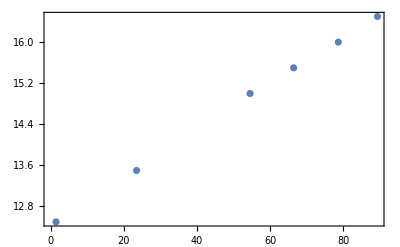

```mathematica
Show[ListPlot[ConstV],Plot[lm[T],{T,-300,100}],Frame->True]
```

```mathematica
Show[ListPlot[ConstV],Plot[lm[T],{T,0,100}],Frame->True]
```

-Graphics-

```mathematica
lm["FitResiduals"]
```

{-0.062817,0.10714,-0.115457,0.0711332}

```mathematica
Show[ListPlot[ConstV],Plot[f[T],{T,0,100}],Frame->True]
```

-Graphics-

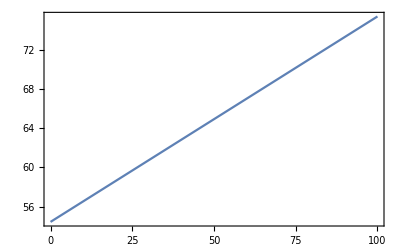

```mathematica
Show[Plot[f[T],{T,0,100}],Frame->True]
```

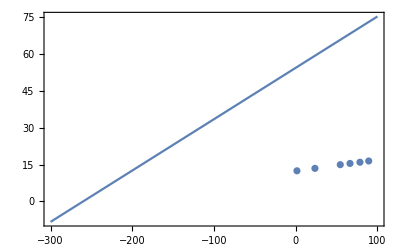

```mathematica
Show[Plot[f[T],{T,-300,100}],ListPlot[ConstV],Frame->True]
```

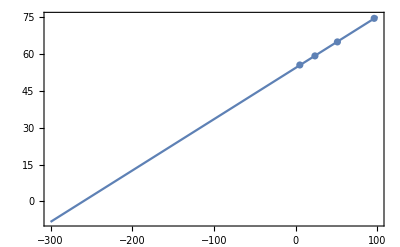

```mathematica
Show[Plot[f[T],{T,-300,100}],ListPlot[ConstP],Frame->True]
```

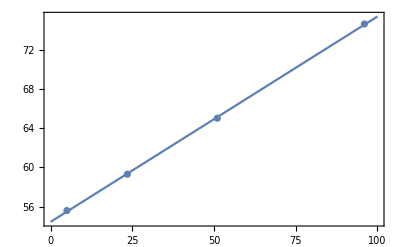

```mathematica
Show[Plot[f[T],{T,0,100}],ListPlot[ConstP],Frame->True]
```

```mathematica
ConstP2= {{23.5,61.7},{5,58.0},{51,67.4},{96,77.0}}
```

{{23.5,61.7},{5,58.},{51,67.4},{96,77.}}

```mathematica
nm=LinearModelFit[ConstP2,T,T]
```

FittedModel[56.8469+0.209187 T]

```mathematica
h[T_]:=Normal[nm]
```

```mathematica
FindRoot[h[T],{T,-300}]
```

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

{T→-271.752}

```mathematica
((-271.752)-(-273.15))/(-273.15)
```

-0.00511807

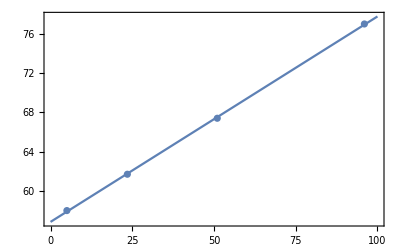

```mathematica
Show[Plot[h[T],{T,0,100}],ListPlot[ConstP2],Frame->True]
```

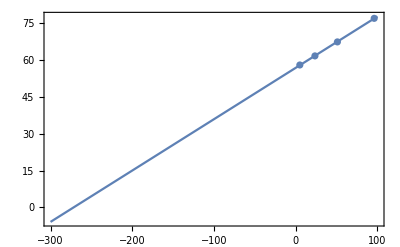

```mathematica
Show[Plot[h[T],{T,-300,100}],ListPlot[ConstP2],Frame->True]
```

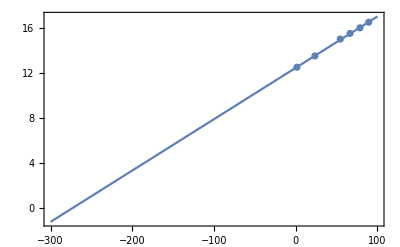

```mathematica
Show[Plot[g[T],{T,-300,100}],ListPlot[ConstV],Frame->True]
```

```mathematica
hm["FitResiduals"]
```

{-0.0185487,-0.0141994,0.0662317,0.02297,-0.0339873,-0.0224663}

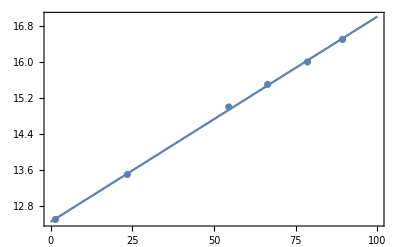

```mathematica
Show[Plot[g[T],{T,0,100}],ListPlot[ConstV],Frame->True]
```

```mathematica
lm["ParameterConfidenceIntervals"]
```

{{53.9924,54.9015},{0.201021,0.217353}}

```mathematica
lm["ParamterTable"]
```

54.4469+0.209187 ParamterTable

```mathematica
hm[{"ParameterTable"}]
```

{ | Estimate | Standard Error | t-Statistic | P-Value
1 | 12.4457 | 0.0339804 | 366.262 | 3.33397×10^-10
T | 0.0456522 | 0.000560072 | 81.5114 | 1.35782×10^-7}

```mathematica
lm[{"ParameterTable"}]
```

{ | Estimate | Standard Error | t-Statistic | P-Value
1 | 54.4469 | 0.105643 | 515.386 | 3.76472×10^-6
T | 0.209187 | 0.00189785 | 110.223 | 0.0000822999}

```mathematica
nm[{"ParameterTable"}]
```

{ | Estimate | Standard Error | t-Statistic | P-Value
1 | 56.8469 | 0.105643 | 538.104 | 3.45355×10^-6
T | 0.209187 | 0.00189785 | 110.223 | 0.0000822999}

```mathematica
ConvP = {{23.5,59.3/59.3},{5,55.6/59.3},{51,65.0/59.3},{96,74.6/59.3}}
```

{{23.5,1.},{5,0.937605},{51,1.09612},{96,1.25801}}

```mathematica
Convlm = LinearModelFit[ConvP, T, T]
```

FittedModel[0.918161+0.0035276 T]

```mathematica
Convlm[{"ParameterTable"}]
```

{ | Estimate | Standard Error | t-Statistic | P-Value
1 | 0.918161 | 0.0017815 | 515.386 | 3.76472×10^-6
T | 0.0035276 | 0.0000320041 | 110.223 | 0.0000822999}

```mathematica
cf[T_]:=Normal[Convlm]
```

```mathematica
FindRoot[cf[T], {T, -300}]
```

{T→-260.279}

```mathematica
(0.0035276*0.5)^2+(0.0017815)^2
```

6.28473×10^-6

```mathematica
(0.00320041)^2
```

0.0000102426

```mathematica
(0.0000320041)^2
```

1.02426×10^-9

```mathematica
(0.0000320041)^2*(-300)^2+(0.0035276*0.5)^2+(0.0017815)^2
```

0.0000984684

```mathematica
(0.0000320041)^2*(100)^2+(0.0035276*0.5)^2+(0.0017815)^2
```

0.0000165274

```mathematica
Sqrt[(0.0035276*0.5)^2+(0.0017815)^2]
```

0.00250694

```mathematica
Sqrt[(0.0000320041)^2*(-300)^2+(0.0035276*0.5)^2+(0.0017815)^2]
```

0.00992312

```mathematica
ConvP2= {{23.5,61.7/61.7},{5,58.0/61.7},{51,67.4/61.7},{96,77.0/61.7}}
```

{{23.5,1.},{5,0.940032},{51,1.09238},{96,1.24797}}

```mathematica
Convnm = LinearModelFit[ConvP2, T, T]
```

FittedModel[0.921344+0.00339039 T]

```mathematica
Convnm[{"ParameterTable"}]
```

{ | Estimate | Standard Error | t-Statistic | P-Value
1 | 0.921344 | 0.00171221 | 538.104 | 3.45355×10^-6
T | 0.00339039 | 0.0000307593 | 110.223 | 0.0000822999}

```mathematica
ch[T_]:=Normal[Convnm]
```

```mathematica
FindRoot[ch[T], {T,-300}]
```

{T→-271.752}

```mathematica
ConvV={{23.5,13.5*6.89475729},{1.5,12.5*6.89475729},{54.5,15*6.89475729},{66.4,15.5*6.89475729},{78.6,16*6.89475729},{89.3,16.5*6.89475729}}
```

{{23.5,93.0792},{1.5,86.1845},{54.5,103.421},{66.4,106.869},{78.6,110.316},{89.3,113.763}}

```mathematica
Convhm = LinearModelFit[ConvV, T, T]
```

FittedModel[85.8102+0.314761 T]

```mathematica
Convhm["ParameterTable"]
```

| Estimate | Standard Error | t-Statistic | P-Value
1 | 85.8102 | 0.234286 | 366.262 | 3.33397×10^-10
T | 0.314761 | 0.00386156 | 81.5114 | 1.35782×10^-7

```mathematica
cg[T_]:=Normal[Convhm]
```

```mathematica
FindRoot[cg[T], {T, -300}]
```

{T→-272.62}

```mathematica
(0.00386156)^2
```

0.0000149116

```mathematica
(0.314761*0.05)^2+(0.234286)^2
```

0.0551376

```mathematica
(0.00386156)^2*(-300)^2+(0.314761*0.05)^2+(0.234286)^2
```

1.39719

```mathematica
(0.00386156)^2*(100)^2+(0.314761*0.05)^2+(0.234286)^2
```

0.204254

```mathematica
Sqrt[(0.314761*0.05)^2+(0.234286)^2]
```

0.234814

```mathematica
Sqrt[(0.00386156)^2*(-300)^2+(0.314761*0.05)^2+(0.234286)^2]
```

1.18203